## Minimize

```mathematica
f=15/(π^4(x^5(Exp[1/x]-1)));
```

```mathematica
{max,val}=Maximize[{f,x≥0},x]
```

{(15 (5+ProductLog[-5/ⅇ^5])^5)/((-1+ⅇ^(5+ProductLog[-5/ⅇ^5])) π^4),{x→1/(5+ProductLog[-5/ⅇ^5])}}

General::munfl: 2.81067×10^23 1.0130909657×10^-21258 is too small to represent as a normalized machine number; precision may be lost.

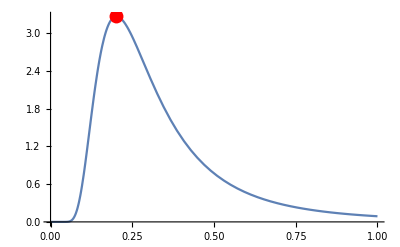

```mathematica
Plot[f,{x,0,1},Epilog->{Red,PointSize[0.025],Point[{x/.val,max}]}]
```

## Linear Programming

c is a linear objective f(x)
m is a matrix of linear constraints
b are bounds for the constraints

```mathematica
c={-1,-2};
m=({{1, 1}, {1, -1}, {-1, -1}, {-1, 1}, {0, 1}, {0, -1}});
```

```mathematica
b={0,0,-1,-1,-0.25,-0.25};
```

```mathematica
sol=LinearProgramming[c,m,b]
```

{0.75,0.25}

```mathematica
Style[constr=And@@MapThread[GreaterEqual,{m.{x,y}ᵀ,b}],Blue,Bold]
```

x+y≥0&&x-y≥0&&-x-y≥-1&&-x+y≥-1&&y≥-0.25&&-y≥-0.25

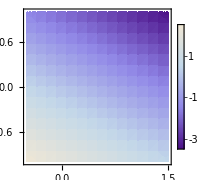

```mathematica
objplot=DensityPlot[c.{x,y},{x,-0.5,1.5},{y,-1,1},ColorFunction->"LakeColors",ImageSize->Small,PlotLegends->True]
```

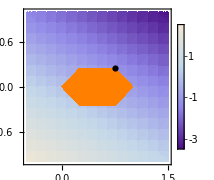

```mathematica
Show[objplot,
RegionPlot[constr,{x,-.5,1.5},{y,-1,1},BoundaryStyle->None,PlotStyle->Orange,ImageSize->Small],
Graphics[{PointSize[0.025],Point@sol}]
]
```

### Exact linear programs

```mathematica
c={1,1};m={{π,2}};b={3};
```

```mathematica
LinearProgramming[c,m,b]
```

{3/π,0}

### Large scale linear programs

```mathematica
c=Range[10^5];
```

```mathematica
m=SparseArray[Table[Band[{1,j 10^4}]->N[j],{j,1,10}],{10^4,10^5}];
```

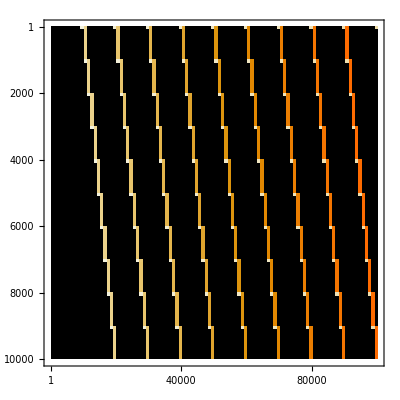

```mathematica
MatrixPlot[m,ColorRules->(0->Black)]
```

```mathematica
b=Range[10^4];
```

```mathematica
sol=LinearProgramming[c,m,b];
```

## Local optimization

```mathematica
f=-Cos[x]/(x^2+6);
```

```mathematica
{min,val}=FindMinimum[f,{x,5}]
```

{-0.0228615,{x→6.00504}}

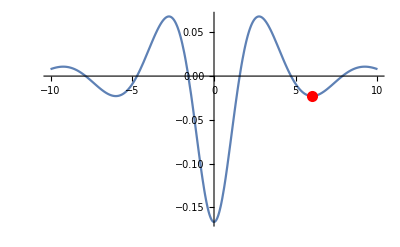

```mathematica
Plot[f,{x,-10,10},PlotRange->All,Epilog-> {Red,PointSize[0.02],Point[{x/.val,min}]}]
```

```mathematica
{min,{x1,x2}}=FindMinimum[(1-X1)^2+100(-X1^2+X2)^2,{{X1,-1.2},{X2,-1.2}}]
```

{0.,{X1→1.,X2→1.}}

```mathematica
Show[Plot3D[(1-X1)^2+100(-X1^2+X2)^2,{X1,-1,1.5},{X2,-1,1.5},PlotStyle->Opacity[0.6],ColorFunction->(Hue[#3]&)],Graphics3D[{Black,PointSize[0.04],Point[{X1/.x1,X2/.x2,min}]}],ImageSize-> Small]
```

-Graphics3D-

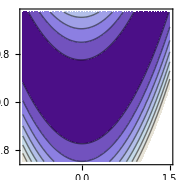

```mathematica
ContourPlot[(1-X1)^2+100(-X1^2+X2)^2,{X1,-1,1.5},{X2,-1,1.5},ColorFunction->"LakeColors",ImageSize->Small]
```

```mathematica
FindMinimum[(1-X1)^2+100(-X1^2+X2)^2,{{X1,-1.2},{X2,-1.2}},StepMonitor:>Print["(X1,X2): ", {X1,X2}]]
```

(X1,X2): {-0.796577,-0.240194}

(X1,X2): {-0.389079,-0.0162315}

(X1,X2): {-0.313527,0.0887007}

(X1,X2): {-0.14356,-0.0072256}

(X1,X2): {-0.0427052,-0.00832815}

(X1,X2): {0.15899,-0.0153524}

(X1,X2): {0.356243,0.0874354}

(X1,X2): {0.544862,0.260647}

(X1,X2): {0.722809,0.490289}

(X1,X2): {0.889576,0.763313}

(X1,X2): {1.,0.987807}

(X1,X2): {1.,1.}

{0.,{X1→1.,X2→1.}}

```mathematica
<<Optimization`UnconstrainedProblems`
```

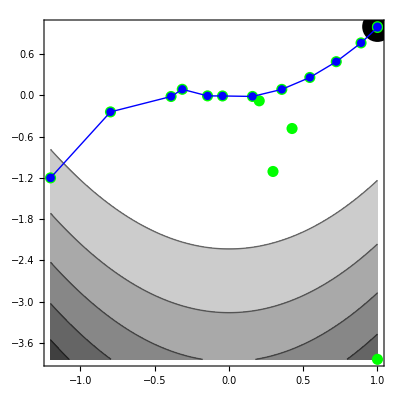
{{0.,{X1→1.,X2→1.}},{Steps→12,Function→17},-Graphics-}

```mathematica
FindMinimumPlot[(1-X1)^2+100(-X1^2+X2)^2,{{X1,-1.2},{X2,-1.2}}]
```

## Global optimization

```mathematica
f=-Cos[x]/(x^2+6);
```

```mathematica
{min,val}=NMinimize[f,{x},Method->"NelderMead"]
```

{-0.166667,{x→-3.30872×10^-24}}

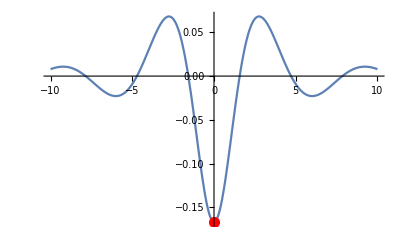

```mathematica
Plot[f,{x,-10,10},PlotRange->All,Epilog-> {Red,PointSize[0.02],Point[{x/.val,min}]}]
```

## Constrained optimization

```mathematica
Plot3D[-1/((x-1)^2+(y-1)^2+1)-2/((x+1)^2+(y+2)^2+1),{x,-10,10},{y,-10,10},PlotPoints->50,PlotRange->All,ColorFunction->"Rainbow",ImageSize->Medium]
```

-Graphics3D-

```mathematica
f={-1/((x-1)^2+(y-1)^2+1)-2/((x+1)^2+(y+2)^2+1),Abs[x]+Abs[y]>1};
```

### With FindMinimum

```mathematica
pts=Reap@FindMinimum[f,{{x,1},{y,-0.5}},StepMonitor:> Sow[{x,y}]]
```

{{-1.14425,{x→0.978937,y→0.968405}},{{{1.,-0.5},{0.999387,-0.464911},{1.62823,0.626921},{0.0858557,0.941013},{1.49306,0.696747},{0.724711,1.16848},{1.11534,0.843606},{0.961082,0.992229},{0.980545,0.969958},{0.979024,0.968494},{0.978938,0.968406},{0.978937,0.968405}}}}

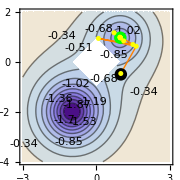

```mathematica
ContourPlot[f[[1]],{x,-3,3},{y,-4,2},ColorFunction->"LakeColors",
RegionFunction->(Abs[#1]+Abs[#2]≥1&),Contours->10,ContourLabels->True,
Epilog->{Orange,Line@pts[[2,1]],Black,PointSize[0.05],Point@pts[[2,1,1]],
Green,Point@pts[[2,1,-1]],PointSize[0.02],Yellow,Point/@Rest[pts[[2,1]]]},
ImageSize->Small
]
```

### With NMinimize

```mathematica
pts=Reap@NMinimize[f,{{x,-2,2},{y,-2,2}},StepMonitor:> Sow[{x,y}]]
```

{{-2.0716,{x→-0.994861,y→-1.99229}},{{{1.51442,0.304803},{-1.47574,-1.40263},{-1.47574,-1.40263},{-1.47574,-1.40263},{-1.47574,-1.40263},{-1.47574,-1.40263},{-1.47574,-1.40263},{-0.95838,-1.43686},{-0.95838,-1.43686},{-0.971999,-1.76026},{-0.971999,-1.76026},{-0.971999,-1.76026},{-0.985617,-2.08366},{-0.985617,-2.08366},{-0.985617,-2.08366},{-0.941688,-2.00295},{-0.986759,-1.9664},{-0.986759,-1.9664},{-1.01999,-1.99762},{-0.989148,-2.00809},{-0.995665,-1.98463},{-0.995665,-1.98463},{-0.99504,-1.99945},{-0.989929,-1.98956},{-0.994075,-1.98957},{-0.993521,-1.99451},{-0.995732,-1.99327},{-0.994351,-1.99173},{-0.994351,-1.99173},{-0.995404,-1.99244},{-0.994415,-1.99238},{-0.99463,-1.99207},{-0.994963,-1.99233},{-0.994963,-1.99233},{-0.994963,-1.99233},{-0.994963,-1.99233},{-0.994837,-1.99225},{-0.994839,-1.99233},{-0.994839,-1.99233},{-0.994854,-1.99228},{-0.994854,-1.99228},{-0.994864,-1.99229},{-0.994861,-1.99229},{-0.994861,-1.99229}}}}

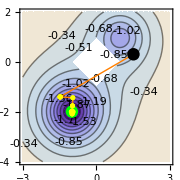

```mathematica
ContourPlot[f[[1]],{x,-3,3},{y,-4,2},ColorFunction->"LakeColors",
RegionFunction->(Abs[#1]+Abs[#2]≥1&),Contours->10,ContourLabels->True,
Epilog->{Orange,Line@pts[[2,1]],Black,PointSize[0.05],Point@pts[[2,1,1]],
Green,Point@pts[[2,1,-1]],PointSize[0.02],Yellow,Point/@Rest[pts[[2,1]]]},ImageSize->Small
]
```

## Constrained optimization

find the value of a for which the solution of y’’(t)+y(t)=3 a sin(y(t)), y(0)=y’(0)=1 has a minimal arc length from t=0 to t=10

```mathematica
psol=ParametricNDSolve[{y''[t]+y[t]==3a Sin[y[t]],y[0]==y'[0]==1,
α'[t]==Sqrt[1+y[t]^2],α[0]==0},{y,α},{t,0,10},{a}]
```

{y→ParametricFunction[<>],α→ParametricFunction[<>]}

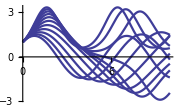

```mathematica
Plot[Table[Evaluate[y[a][t]/.psol],{a,0,1,0.1}],{t,0,10},PlotStyle->(ColorData[1][1]),ImageSize->Small]
```

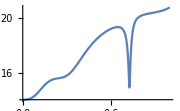

```mathematica
Plot[Evaluate[α[a][10]/.psol],{a,0,1},ImageSize->Small]
```

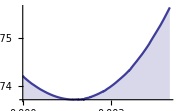

```mathematica
Plot[Evaluate[α[a][10]/.psol],{a,0,0.005},ImageSize->Small,PlotStyle->ColorData[1][1],Filling->Bottom]
```

### global minima

```mathematica
gmin0=NMinimize[{α[a][10]/.psol,0.≤a≤ 0.005},{a},AccuracyGoal->7]
```

{14.0174,{a→0.00189029}}

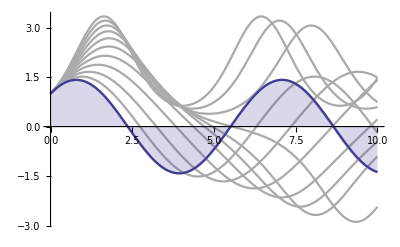

```mathematica
Show[
Plot[Table[Evaluate[y[a][t]/.psol],{a,0,1,0.1}],{t,0,10},PlotStyle->Lighter@Gray],
Plot[Evaluate[y[a/.gmin0[[-1]] ][t]/.psol],{t,0,10},PlotStyle->ColorData[1][1],Filling->Axis]
]
```

### local minima

```mathematica
lmin0=FindMinimum[{α[a][10]/.psol,0<a<1},{a,0.7},AccuracyGoal->7]
```

{14.9146,{a→0.725089}}

```mathematica
fns=Table[Evaluate[y[a][t]/.psol],{a,0.65,0.8,0.005}];
```

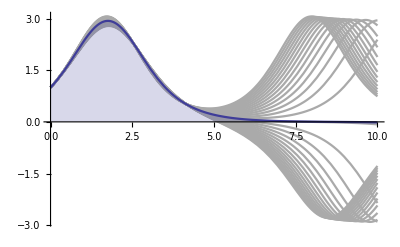

```mathematica
Show[
Plot[fns,{t,0,10},PlotStyle->Lighter@Gray],
Plot[Evaluate[y[a/.lmin0[[-1]] ][t]/.psol],{t,0,10},PlotStyle->ColorData[1][1],Filling->Axis]
]
```

## Linear Solve

```mathematica
A=ExampleData[{"Matrix","Boeing/msc04515"}];
```

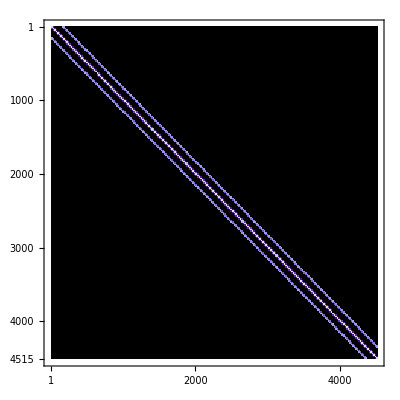

```mathematica
MatrixPlot[A,ColorFunction->"LakeColors",ColorRules->(0-> Black)]
```

```mathematica
b=RandomReal[1,Length[A]];
```

```mathematica
AbsoluteTiming[sol=LinearSolve[A,b];]
```

{0.0767641,Null}

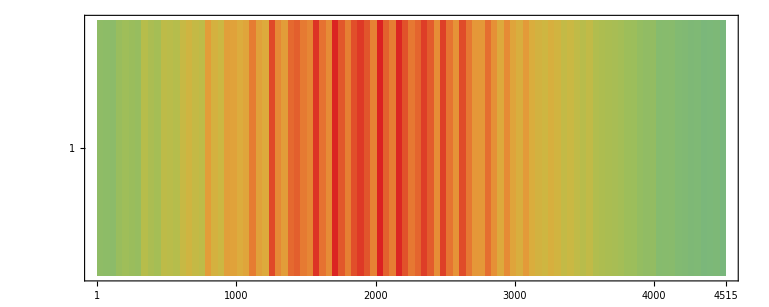

```mathematica
MatrixPlot[{sol},ColorFunction->"Rainbow"]
```

```mathematica
Sn=Normal[A];
```

```mathematica
N[ByteCount[Sn]/ByteCount[A]]
```

101.858

```mathematica
AbsoluteTiming[ex=LinearSolve[Sn,b];]
```

{0.652116,Null}

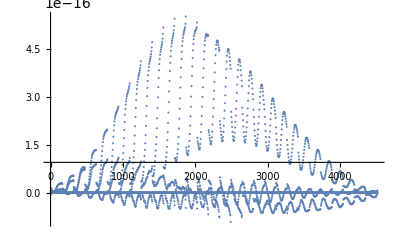

```mathematica
ListPlot[ex-sol,PlotRange->All]
```